```mathematica
Quit[]
```

```mathematica
(*Ansatz*)
dim=4;
x={t,r,θ,φ};
BISERIES[Z_]:=Z/.Union[{S2'[θ]^2->4 S2[θ](1-S2[θ]),S2''[θ]->2 (1-2S2[θ])}]//Simplify
gdd={{-α[t, r]^2,0,0,0},{0,A[t,r]^2,0,0},{0,0,r^2,0},{0,0,0,r^2 S2[θ]}};(*gdowndown or metric*)
guu=Simplify[Inverse[gdd]];
g=Simplify[Det[gdd]];
SQRTg=√-g//Simplify;
ϕ=ϕ0[t,r];
```

```mathematica
(*Metric tensors*)
christ=BISERIES[Table[1/2 Sum[guu[[l4,l1]](D[gdd[[l2,l1]],x[[l3]]]+D[gdd[[l1,l3]],x[[l2]]]-D[gdd[[l2,l3]],x[[l1]]]),{l1,1,dim}],{l2,1,dim},{l3,1,dim},{l4,1,dim}]];(*which index is up index?* Its the final index?*)
```

```mathematica
Ruddd=BISERIES[Table[D[christ[[l2,m2,l1]],x[[m1]]]-D[christ[[l2,m1,l1]],x[[m2]]]+Sum[-christ[[k,m2,l1]]christ[[l2,m1,k]]+christ[[k,m1,l1]]christ[[l2,m2,k]],{k,1,dim}],{l1,1,dim},{l2,1,dim},{m1,1,dim},{m2,1,dim}]]; (* Subscript[R^l1, l2 m1 m2] = Subscript[Γ^l1, l2 m2,m1] - Subscript[Γ^l1, l2 m1,m2] - Subscript[Γ^l1, k m2] Subscript[Γ^k, l2 m1] + Subscript[Γ^l1, k m1] Subscript[Γ^k, l2 m2] *)
```

```mathematica
Rdddd=BISERIES[Table[Sum[gdd[[a1,b1]]Ruddd[[b1,a2,a3,a4]],{b1,dim}],{a1,dim},{a2,dim},{a3,dim},{a4,dim}]];
Rdd=BISERIES[Table[Sum[Ruddd[[k,l1,k,l2]],{k,1,dim}],{l1,1,dim},{l2,1,dim}]];
R=BISERIES[Sum[Rdd[[l1,l2]]guu[[l1,l2]],{l1,1,dim},{l2,1,dim}]];
```

```mathematica
X = -1/2 Sum[guu[[b1,b2]]D[ϕ,x[[b1]]]D[ϕ,x[[b2]]],{b1,dim},{b2,dim}];
```

```mathematica
Clear[f]
(*Scalar field Stress-Energy Tensor*)
TϕTTdd=BISERIES[Table[1/2 ( gdd[[a1,a2]] *(X-β X^2 +γ X^3)   + (1 - 2 β X+ 3γ X^2)D[ϕ,x[[a1]]]D[ϕ,x[[a2]]]) ,{a1,dim},{a2,dim}]];(*added cubic term in K(x)*)
```

```mathematica
(*Equations of motion*)
BOXphi=BISERIES[1/SQRTg Sum[D[SQRTg guu[[i,j]]D[ϕ,x[[j]]],x[[i]]],{i,1,dim},{j,1,dim}]];
RHS=0;
(*myRHS = -2β/(1 - 2β X) Sum[Sum[guu[[i, k]] guu[j, l]D[ϕ, x[[k]]]  D[ϕ, x[[l]]] ,{k, 1, dim},{l, 1, dim}]  D[D[ϕ, x[[i]]], x[[j]]] +Sum[christ[[ i, j, h]] D[ϕ, x[[h]]], {h, 1, dim}] , {i, 1, dim}, {j, 1,dim}]; ()*)
Edd=BISERIES[Rdd-1/2 gdd R-TϕTTdd];
Eϕ=BISERIES[BOXphi-RHS];
```

```mathematica
(*d2xxG2(X)/(1+ dxG2(X)) d^u phi d^v phi Del_u[Del_v[phi]] = -2b/(1-2bX) d/du phi d/dv phi (nabla [d_u phi - Tabc ]])*)
```

```mathematica
myRHS =  (-2β +6 γ X)/(1 - 2β X+ 3γ X^2)Sum[  Sum[guu[[a, i]] D[ϕ, x[[a]]],{a, 1,dim} ]  Sum[guu[[b, j]]D[ϕ, x[[b]]],{b, 1, dim}] (D[ϕ,{x[[j]]}, {x[[i]]} ]    -   Sum[christ[[ i, j, k]] D[ϕ, x[[k]]], {k, 1, dim}  ]) , {i, 1, dim},{j, 1,dim}];
```

```mathematica
myEϕ = BISERIES[BOXphi-myRHS] (*dtPI*)
```

-(A^(0,1)[t,r] ϕ0^(0,1)[t,r])/A[t,r]^3+((2/r+(α^(0,1)[t,r])/α[t,r]) ϕ0^(0,1)[t,r]+ϕ0^(0,2)[t,r])/A[t,r]^2-(A^(1,0)[t,r] ϕ0^(1,0)[t,r])/(A[t,r] α[t,r]^2)+(α^(1,0)[t,r] ϕ0^(1,0)[t,r]-α[t,r] ϕ0^(2,0)[t,r])/α[t,r]^3+(4 (3 γ α[t,r]^2 (ϕ0^(0,1)[t,r])^2+A[t,r]^2 (2 β α[t,r]^2-3 γ (ϕ0^(1,0)[t,r])^2)) (α[t,r]^5 (ϕ0^(0,1)[t,r])^2 (-A^(0,1)[t,r] ϕ0^(0,1)[t,r]+A[t,r] ϕ0^(0,2)[t,r])+A[t,r]^3 α[t,r]^2 α^(0,1)[t,r] ϕ0^(0,1)[t,r] (ϕ0^(1,0)[t,r])^2-A[t,r]^5 α^(1,0)[t,r] (ϕ0^(1,0)[t,r])^3+A[t,r]^2 α[t,r]^3 ϕ0^(0,1)[t,r] ϕ0^(1,0)[t,r] (ϕ0^(0,1)[t,r] A^(1,0)[t,r]-2 A[t,r] ϕ0^(1,1)[t,r])+A[t,r]^5 α[t,r] (ϕ0^(1,0)[t,r])^2 ϕ0^(2,0)[t,r]))/(3 γ A[t,r]^3 α[t,r]^7 (ϕ0^(0,1)[t,r])^4+2 A[t,r]^5 α[t,r]^5 (ϕ0^(0,1)[t,r])^2 (2 β α[t,r]^2-3 γ (ϕ0^(1,0)[t,r])^2)+A[t,r]^7 (4 α[t,r]^7-4 β α[t,r]^5 (ϕ0^(1,0)[t,r])^2+3 γ α[t,r]^3 (ϕ0^(1,0)[t,r])^4))

```mathematica
(*dphi/dr = PHI Q here   and dphi/dt = alpha/a PI*)
```

```mathematica
sostϕt={D[ϕ0[t,r],t]->α[t,r]/A[t,r]P[t,r]};  (*dphi/dt = alpha/a P *)
sostϕr={D[ϕ0[t,r],r]->Q[t,r]};   (*dphi/dr = Q*)
(*Solve for dPHI/dt =  f (A, alpha, PI, PI', alpha', A')*)
```

```mathematica
EQ1=(D[ϕ0[t,r],{t},{r}]/.D[sostϕr,t])-(D[ϕ0[t,r],{t},{r}]/.D[sostϕt,r])//Simplify ;(*D[f, {x},{y}] = d^2f/dxdy*)
sQt=Solve[EQ1==0,D[Q[t,r],t]][[1]]//Simplify  (*here we get expression of dPHI/dt pf PHI dot*)
```

{Q^(1,0)[t,r]→(A[t,r] α[t,r] P^(0,1)[t,r]+P[t,r] (-α[t,r] A^(0,1)[t,r]+A[t,r] α^(0,1)[t,r]))/A[t,r]^2}

```mathematica
(*here we compute dPI/dt  = f(PHI, A, alp and there derivs )* Ephi is equation of motion for the scalar field)
```

```mathematica
EP1=Collect[myEϕ//.Union[sostϕt,sostϕr,D[sostϕt,t],D[sostϕr,r]],{D[P[t,r],t],D[α[t,r],{t,2}],D[α[t,r],{t,1}],D[A[t,r],r],D[Q[t,r],r],r,η},Simplify];
sPt=Solve[EP1==0,D[P[t,r],t]][[1]]//Simplify
```

{P^(1,0)[t,r]→(-3 r γ Q[t,r] (P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+5 Q[t,r]^4) α[t,r] A^(0,1)[t,r]+4 A[t,r]^5 (r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r]))+3 γ A[t,r] (P[t,r]^2-Q[t,r]^2) (P[t,r]^2 (r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]-3 r α^(0,1)[t,r]))-Q[t,r]^2 (5 r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r]))+4 r P[t,r]^3 A^(1,0)[t,r]-4 r P[t,r] Q[t,r]^2 A^(1,0)[t,r])+4 β A[t,r]^3 (P[t,r]^2 (-r α[t,r] Q^(0,1)[t,r]+Q[t,r] (-2 α[t,r]+r α^(0,1)[t,r]))+Q[t,r]^2 (3 r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r]))-2 r P[t,r]^3 A^(1,0)[t,r]+2 r P[t,r] Q[t,r]^2 A^(1,0)[t,r])-4 r A[t,r]^4 Q[t,r] (α[t,r] A^(0,1)[t,r]+4 β P[t,r] ϕ0^(1,1)[t,r])+4 r A[t,r]^2 Q[t,r] (β P[t,r]^2 α[t,r] A^(0,1)[t,r]-3 β Q[t,r]^2 α[t,r] A^(0,1)[t,r]+6 γ P[t,r]^3 ϕ0^(1,1)[t,r]-6 γ P[t,r] Q[t,r]^2 ϕ0^(1,1)[t,r]))/(r A[t,r]^2 (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)))}

```mathematica
sPt/.{γ->0}
```

{P^(1,0)[t,r]→(4 r A[t,r]^2 Q[t,r] (β P[t,r]^2 α[t,r] A^(0,1)[t,r]-3 β Q[t,r]^2 α[t,r] A^(0,1)[t,r])+4 A[t,r]^5 (r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r]))+4 β A[t,r]^3 (P[t,r]^2 (-r α[t,r] Q^(0,1)[t,r]+Q[t,r] (-2 α[t,r]+r α^(0,1)[t,r]))+Q[t,r]^2 (3 r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r]))-2 r P[t,r]^3 A^(1,0)[t,r]+2 r P[t,r] Q[t,r]^2 A^(1,0)[t,r])-4 r A[t,r]^4 Q[t,r] (α[t,r] A^(0,1)[t,r]+4 β P[t,r] ϕ0^(1,1)[t,r]))/(r A[t,r]^2 (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)))}

```mathematica
aeq = (r β Q[t,r] (P[t,r]^2-3 Q[t,r]^2) α[t,r] Derivative[0,1][A][t,r]+A[t,r]^3 (r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r]))+β A[t,r] (P[t,r]^2 (-r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (-2 α[t,r]+r Derivative[0,1][α][t,r]))+Q[t,r]^2 (3 r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r]))-2 r P[t,r]^3 Derivative[1,0][A][t,r]+2 r P[t,r] Q[t,r]^2 Derivative[1,0][A][t,r])-r A[t,r]^2 Q[t,r] (α[t,r] Derivative[0,1][A][t,r]+4 β P[t,r] Derivative[1,1][ϕ0][t,r]))/(r A[t,r]^2 (A[t,r]^2+β (-3 P[t,r]^2+Q[t,r]^2)));(*Laura eq*)
beq = (4 r A[t,r]^2 Q[t,r] (β P[t,r]^2 α[t,r] Derivative[0,1][A][t,r]-3 β Q[t,r]^2 α[t,r] Derivative[0,1][A][t,r])+4 A[t,r]^5 (r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r]))+4 β A[t,r]^3 (P[t,r]^2 (-r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (-2 α[t,r]+r Derivative[0,1][α][t,r]))+Q[t,r]^2 (3 r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r]))-2 r P[t,r]^3 Derivative[1,0][A][t,r]+2 r P[t,r] Q[t,r]^2 Derivative[1,0][A][t,r])-4 r A[t,r]^4 Q[t,r] (α[t,r] Derivative[0,1][A][t,r]+4 β P[t,r] Derivative[1,1][ϕ0][t,r]))/(r A[t,r]^2 (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2))); (*Cubic eq γ->0*)
FullSimplify[aeq-beq]
```

0

```mathematica
simpleEqCubic = sPt/.{Derivative[1,1][ϕ0][t,r]-> (A[t,r] α[t,r] Derivative[0,1][P][t,r]+P[t,r] (-α[t,r] Derivative[0,1][A][t,r]+A[t,r] Derivative[0,1][α][t,r]))/A[t,r]^2, Derivative[1,0][A][t,r]->(r P[t,r] Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(16 A[t,r]^4)}
```

{P^(1,0)[t,r]→(-3 r γ Q[t,r] (P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+5 Q[t,r]^4) α[t,r] A^(0,1)[t,r]+4 A[t,r]^5 (r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r]))+4 β A[t,r]^3 (-(r^2 P[t,r]^4 Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(8 A[t,r]^4)+(r^2 P[t,r]^2 Q[t,r]^3 (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(8 A[t,r]^4)+P[t,r]^2 (-r α[t,r] Q^(0,1)[t,r]+Q[t,r] (-2 α[t,r]+r α^(0,1)[t,r]))+Q[t,r]^2 (3 r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r])))+3 γ A[t,r] (P[t,r]^2-Q[t,r]^2) ((r^2 P[t,r]^4 Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(4 A[t,r]^4)-(r^2 P[t,r]^2 Q[t,r]^3 (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(4 A[t,r]^4)+P[t,r]^2 (r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]-3 r α^(0,1)[t,r]))-Q[t,r]^2 (5 r α[t,r] Q^(0,1)[t,r]+Q[t,r] (2 α[t,r]+r α^(0,1)[t,r])))-4 r A[t,r]^4 Q[t,r] (α[t,r] A^(0,1)[t,r]+(4 β P[t,r] (A[t,r] α[t,r] P^(0,1)[t,r]+P[t,r] (-α[t,r] A^(0,1)[t,r]+A[t,r] α^(0,1)[t,r])))/A[t,r]^2)+4 r A[t,r]^2 Q[t,r] (β P[t,r]^2 α[t,r] A^(0,1)[t,r]-3 β Q[t,r]^2 α[t,r] A^(0,1)[t,r]+(6 γ P[t,r]^3 (A[t,r] α[t,r] P^(0,1)[t,r]+P[t,r] (-α[t,r] A^(0,1)[t,r]+A[t,r] α^(0,1)[t,r])))/A[t,r]^2-(6 γ P[t,r] Q[t,r]^2 (A[t,r] α[t,r] P^(0,1)[t,r]+P[t,r] (-α[t,r] A^(0,1)[t,r]+A[t,r] α^(0,1)[t,r])))/A[t,r]^2))/(r A[t,r]^2 (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)))}

```mathematica
AaEq = (-3 r γ Q[t,r] (P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+5 Q[t,r]^4) α[t,r] Derivative[0,1][A][t,r]+4 A[t,r]^5 (r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r]))+4 β A[t,r]^3 (-(r^2 P[t,r]^4 Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(8 A[t,r]^4)+(r^2 P[t,r]^2 Q[t,r]^3 (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(8 A[t,r]^4)+P[t,r]^2 (-r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (-2 α[t,r]+r Derivative[0,1][α][t,r]))+Q[t,r]^2 (3 r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r])))+3 γ A[t,r] (P[t,r]^2-Q[t,r]^2) ((r^2 P[t,r]^4 Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(4 A[t,r]^4)-(r^2 P[t,r]^2 Q[t,r]^3 (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(4 A[t,r]^4)+P[t,r]^2 (r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]-3 r Derivative[0,1][α][t,r]))-Q[t,r]^2 (5 r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r])))-4 r A[t,r]^4 Q[t,r] (α[t,r] Derivative[0,1][A][t,r]+(4 β P[t,r] (A[t,r] α[t,r] Derivative[0,1][P][t,r]+P[t,r] (-α[t,r] Derivative[0,1][A][t,r]+A[t,r] Derivative[0,1][α][t,r])))/A[t,r]^2)+4 r A[t,r]^2 Q[t,r] (β P[t,r]^2 α[t,r] Derivative[0,1][A][t,r]-3 β Q[t,r]^2 α[t,r] Derivative[0,1][A][t,r]+(6 γ P[t,r]^3 (A[t,r] α[t,r] Derivative[0,1][P][t,r]+P[t,r] (-α[t,r] Derivative[0,1][A][t,r]+A[t,r] Derivative[0,1][α][t,r])))/A[t,r]^2-(6 γ P[t,r] Q[t,r]^2 (A[t,r] α[t,r] Derivative[0,1][P][t,r]+P[t,r] (-α[t,r] Derivative[0,1][A][t,r]+A[t,r] Derivative[0,1][α][t,r])))/A[t,r]^2))/(r A[t,r]^2 (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)));
AbEq = (r β Q[t,r] (P[t,r]^2-3 Q[t,r]^2) α[t,r] Derivative[0,1][A][t,r]+A[t,r]^3 (r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r]))+β A[t,r] (-(r^2 P[t,r]^4 Q[t,r] (A[t,r]^2+β (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(2 A[t,r]^2)+(r^2 P[t,r]^2 Q[t,r]^3 (A[t,r]^2+β (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(2 A[t,r]^2)+P[t,r]^2 (-r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (-2 α[t,r]+r Derivative[0,1][α][t,r]))+Q[t,r]^2 (3 r α[t,r] Derivative[0,1][Q][t,r]+Q[t,r] (2 α[t,r]+r Derivative[0,1][α][t,r])))-r A[t,r]^2 Q[t,r] (α[t,r] Derivative[0,1][A][t,r]+(4 β P[t,r] (A[t,r] α[t,r] Derivative[0,1][P][t,r]+P[t,r] (-α[t,r] Derivative[0,1][A][t,r]+A[t,r] Derivative[0,1][α][t,r])))/A[t,r]^2))/(r A[t,r]^2 (A[t,r]^2+β (-3 P[t,r]^2+Q[t,r]^2)));
```

```mathematica
FullSimplify[AaEq - AbEq](*/.{γ->0}*)
```

-((3 γ (P[t,r]^2-Q[t,r]^2) α[t,r] (3 r^2 β γ P[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^3 (3 P[t,r]^2-Q[t,r]^2)-r^2 A[t,r]^2 P[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 ((8 β^2+3 γ) P[t,r]^2-(4 β^2+3 γ) Q[t,r]^2)+16 r A[t,r]^5 Q[t,r] (P[t,r]^2-Q[t,r]^2) A^(0,1)[t,r]-8 r β A[t,r]^3 Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 A^(0,1)[t,r]+4 A[t,r]^6 (P[t,r] Q[t,r] (-r^2 P[t,r]^3+P[t,r] (8+r^2 Q[t,r]^2)-8 r P^(0,1)[t,r])+4 r (P[t,r]^2+Q[t,r]^2) Q^(0,1)[t,r])+8 β A[t,r]^4 (P[t,r] Q[t,r] (P[t,r]^2-Q[t,r]^2) (P[t,r] (-2+r^2 (P[t,r]^2-Q[t,r]^2))+2 r P^(0,1)[t,r])+r (-P[t,r]^4+Q[t,r]^4) Q^(0,1)[t,r])))/(4 r A[t,r]^5 (A[t,r]^2+β (-3 P[t,r]^2+Q[t,r]^2)) (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4))))

```mathematica
FullSimplify[AaEq - AbEq]/.{ Derivative[0,1][A][t,r]->1/(32 r A[t,r]^3)(-16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 r^2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+4 A[t,r]^4 (4+r^2 (P[t,r]^2+Q[t,r]^2)))}
```

-((3 γ (P[t,r]^2-Q[t,r]^2) α[t,r] (3 r^2 β γ P[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^3 (3 P[t,r]^2-Q[t,r]^2)-r^2 A[t,r]^2 P[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 ((8 β^2+3 γ) P[t,r]^2-(4 β^2+3 γ) Q[t,r]^2)+1/2 A[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2) (-16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 r^2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+4 A[t,r]^4 (4+r^2 (P[t,r]^2+Q[t,r]^2)))-1/4 β Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 (-16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 r^2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+4 A[t,r]^4 (4+r^2 (P[t,r]^2+Q[t,r]^2)))+4 A[t,r]^6 (P[t,r] Q[t,r] (-r^2 P[t,r]^3+P[t,r] (8+r^2 Q[t,r]^2)-8 r P^(0,1)[t,r])+4 r (P[t,r]^2+Q[t,r]^2) Q^(0,1)[t,r])+8 β A[t,r]^4 (P[t,r] Q[t,r] (P[t,r]^2-Q[t,r]^2) (P[t,r] (-2+r^2 (P[t,r]^2-Q[t,r]^2))+2 r P^(0,1)[t,r])+r (-P[t,r]^4+Q[t,r]^4) Q^(0,1)[t,r])))/(4 r A[t,r]^5 (A[t,r]^2+β (-3 P[t,r]^2+Q[t,r]^2)) (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4))))

```mathematica
TryNeu = Expand[-(3 γ (P[t,r]^2-Q[t,r]^2) α[t,r] (3 r^2 β γ P[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^3 (3 P[t,r]^2-Q[t,r]^2)-r^2 A[t,r]^2 P[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 ((8 β^2+3 γ) P[t,r]^2-(4 β^2+3 γ) Q[t,r]^2)+1/2 A[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2) (-16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 r^2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+4 A[t,r]^4 (4+r^2 (P[t,r]^2+Q[t,r]^2)))-1/4 β Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 (-16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 r^2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+4 A[t,r]^4 (4+r^2 (P[t,r]^2+Q[t,r]^2)))+4 A[t,r]^6 (P[t,r] Q[t,r] (-r^2 P[t,r]^3+P[t,r] (8+r^2 Q[t,r]^2)-8 r Derivative[0,1][P][t,r])+4 r (P[t,r]^2+Q[t,r]^2) Derivative[0,1][Q][t,r])+8 β A[t,r]^4 (P[t,r] Q[t,r] (P[t,r]^2-Q[t,r]^2) (P[t,r] (-2+r^2 (P[t,r]^2-Q[t,r]^2))+2 r Derivative[0,1][P][t,r])+r (-P[t,r]^4+Q[t,r]^4) Derivative[0,1][Q][t,r])))]//FullSimplify;
TryDen = Expand[(4 r A[t,r]^5 (A[t,r]^2+β (-3 P[t,r]^2+Q[t,r]^2)) (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)))]//FullSimplify;
FullSimplify[TryNeu/TryDen ]
```

```mathematica
CForm[(3 γ (P[t,r]^2-Q[t,r]^2) α[t,r] (32 A[t,r]^8 Q[t,r] (P[t,r]^2-Q[t,r]^2)+r^2 β γ Q[t,r] (-P[t,r]^2+Q[t,r]^2)^3 (31 P[t,r]^4-8 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+2 r^2 A[t,r]^2 Q[t,r] (P[t,r]^2-Q[t,r]^2)^2 ((13 β^2+γ) P[t,r]^4-2 (3 β^2+γ) P[t,r]^2 Q[t,r]^2+(β^2+γ) Q[t,r]^4)+8 A[t,r]^6 (Q[t,r] ((r^2-2 β) P[t,r]^4+4 Q[t,r]^2+(r^2-2 β) Q[t,r]^4-2 P[t,r]^2 (10+(r^2-2 β) Q[t,r]^2)+16 r P[t,r] Derivative[0,1][P][t,r])-8 r (P[t,r]^2+Q[t,r]^2) Derivative[0,1][Q][t,r])+8 β A[t,r]^4 (Q[t,r] (-P[t,r]^2+Q[t,r]^2) (2 r^2 P[t,r]^4+2 Q[t,r]^2+r^2 Q[t,r]^4-P[t,r]^2 (10+3 r^2 Q[t,r]^2)+8 r P[t,r] Derivative[0,1][P][t,r])+4 r (P[t,r]^4-Q[t,r]^4) Derivative[0,1][Q][t,r])))/(16 r A[t,r]^5 (A[t,r]^2+β (-3 P[t,r]^2+Q[t,r]^2)) (4 A[t,r]^4+4 β A[t,r]^2 (-3 P[t,r]^2+Q[t,r]^2)+3 γ (5 P[t,r]^4-6 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)))]
```

(3*γ*(Power(P(t,r),2) - Power(Q(t,r),2))*α(t,r)*(32*Power(A(t,r),8)*Q(t,r)*(Power(P(t,r),2) - Power(Q(t,r),2)) + 
       Power(r,2)*β*γ*Q(t,r)*Power(-Power(P(t,r),2) + Power(Q(t,r),2),3)*(31*Power(P(t,r),4) - 8*Power(P(t,r),2)*Power(Q(t,r),2) + Power(Q(t,r),4)) + 
       2*Power(r,2)*Power(A(t,r),2)*Q(t,r)*Power(Power(P(t,r),2) - Power(Q(t,r),2),2)*
        ((13*Power(β,2) + γ)*Power(P(t,r),4) - 2*(3*Power(β,2) + γ)*Power(P(t,r),2)*Power(Q(t,r),2) + (Power(β,2) + γ)*Power(Q(t,r),4)) + 
       8*Power(A(t,r),6)*(Q(t,r)*((Power(r,2) - 2*β)*Power(P(t,r),4) + 4*Power(Q(t,r),2) + (Power(r,2) - 2*β)*Power(Q(t,r),4) - 
             2*Power(P(t,r),2)*(10 + (Power(r,2) - 2*β)*Power(Q(t,r),2)) + 16*r*P(t,r)*Derivative(0,1)(P)(t,r)) - 
          8*r*(Power(P(t,r),2) + Power(Q(t,r),2))*Derivative(0,1)(Q)(t,r)) + 
       8*β*Power(A(t,r),4)*(Q(t,r)*(-Power(P(t,r),2) + Power(Q(t,r),2))*
           (2*Power(r,2)*Power(P(t,r),4) + 2*Power(Q(t,r),2) + Power(r,2)*Power(Q(t,r),4) - Power(P(t,r),2)*(10 + 3*Power(r,2)*Power(Q(t,r),2)) + 
             8*r*P(t,r)*Derivative(0,1)(P)(t,r)) + 4*r*(Power(P(t,r),4) - Power(Q(t,r),4))*Derivative(0,1)(Q)(t,r))))/
   (16.*r*Power(A(t,r),5)*(Power(A(t,r),2) + β*(-3*Power(P(t,r),2) + Power(Q(t,r),2)))*
     (4*Power(A(t,r),4) + 4*β*Power(A(t,r),2)*(-3*Power(P(t,r),2) + Power(Q(t,r),2)) + 3*γ*(5*Power(P(t,r),4) - 6*Power(P(t,r),2)*Power(Q(t,r),2) + Power(Q(t,r),4))))

Case Minkowski

```mathematica
α[t_,r_]:=1;
A[t_,r_]:=1;
S2[θ_]:=Sin[θ]^2;
```

```mathematica
EQ
```

-P^(0,1)[t,r]+Q^(1,0)[t,r]

```mathematica
EP
```

-(2 Q[t,r])/r-Q^(0,1)[t,r]+P^(1,0)[t,r]

```mathematica
-1/r^2 D[r^2 Q[t,r],r]//Simplify
```

-(2 Q[t,r])/r-Q^(0,1)[t,r]

```mathematica
sostϕr
sostϕt
```

{ϕ0^(0,1)[t,r]→Q[t,r]}

{ϕ0^(1,0)[t,r]→P[t,r]}

General case

```mathematica
Ett=Collect[Edd[[1,1]]//.Union[sostϕt,sostϕr,D[sostϕt,t],D[sostϕr,r],D[sostϕr,t]],{D[B[t,r],r],η,r},Simplify]
Etr=Collect[Edd[[1,2]]//.Union[sostϕt,sostϕr,D[sostϕt,t],D[sostϕr,r],D[sostϕr,t],sQt],{D[B[t,r],t],η,r},Simplify];
Err=Collect[Edd[[2,2]]//.Union[sostϕt,sostϕr,D[sostϕt,t],D[sostϕr,r],D[sostϕr,t]],{D[A[t,r],r],η,r},Simplify]
Eθθ=Collect[Edd[[3,3]]//.Union[sostϕt,sostϕr,D[sostϕt,t],D[sostϕr,r],D[sostϕr,t],sQt],{D[B[t,r],{t,2}],D[Q[t,r],r],D[P[t,r],t],D[A[t,r],{r,2}],D[B[t,r],t],D[A[t,r],t],D[A[t,r],r],η,r},Simplify];
```

((1-1/A[t,r]^2) α[t,r]^2)/r^2-1/(16 A[t,r]^6)(4 A[t,r]^4 (P[t,r]^2+Q[t,r]^2)+γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)) α[t,r]^2+(2 α[t,r]^2 A^(0,1)[t,r])/(r A[t,r]^3)

(1-A[t,r]^2)/r^2-1/(16 A[t,r]^4)(4 A[t,r]^4 (P[t,r]^2+Q[t,r]^2)+γ (P[t,r]^2-Q[t,r]^2)^2 (P[t,r]^2+5 Q[t,r]^2)-2 β A[t,r]^2 (P[t,r]^4+2 P[t,r]^2 Q[t,r]^2-3 Q[t,r]^4))+(2 α^(0,1)[t,r])/(r α[t,r])

```mathematica
Ealp=Collect[Err,{D[α[t,r],r],r},Simplify]
EA=Collect[Ett,{D[A[t,r],r],r},Simplify]
```

(1-A[t,r]^2)/r^2-1/(16 A[t,r]^4)(4 A[t,r]^4 (P[t,r]^2+Q[t,r]^2)+γ (P[t,r]^2-Q[t,r]^2)^2 (P[t,r]^2+5 Q[t,r]^2)-2 β A[t,r]^2 (P[t,r]^4+2 P[t,r]^2 Q[t,r]^2-3 Q[t,r]^4))+(2 α^(0,1)[t,r])/(r α[t,r])

((1-1/A[t,r]^2) α[t,r]^2)/r^2-1/(16 A[t,r]^6)(4 A[t,r]^4 (P[t,r]^2+Q[t,r]^2)+γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)) α[t,r]^2+(2 α[t,r]^2 A^(0,1)[t,r])/(r A[t,r]^3)

```mathematica
Solve[Ealp == 0, Derivative[0,1][α][t,r]]//FullSimplify
```

{{α^(0,1)[t,r]→1/(32 r A[t,r]^4)(16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (P[t,r]^2+5 Q[t,r]^2)-2 r^2 β A[t,r]^2 (P[t,r]^4+2 P[t,r]^2 Q[t,r]^2-3 Q[t,r]^4)+4 A[t,r]^4 (-4+r^2 (P[t,r]^2+Q[t,r]^2))) α[t,r]}}

```mathematica
Solve[EA == 0, Derivative[0,1][A][t,r]]//FullSimplify
```

{{A^(0,1)[t,r]→1/(32 r A[t,r]^3)(-16 A[t,r]^6+r^2 γ (P[t,r]^2-Q[t,r]^2)^2 (5 P[t,r]^2+Q[t,r]^2)+2 r^2 β A[t,r]^2 (-3 P[t,r]^4+2 P[t,r]^2 Q[t,r]^2+Q[t,r]^4)+4 A[t,r]^4 (4+r^2 (P[t,r]^2+Q[t,r]^2)))}}

```mathematica
EqdtA=Collect[Etr,{D[A[t,r],t],r},Simplify]
```

-(P[t,r] Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(8 A[t,r]^5)+(2 A^(1,0)[t,r])/(r A[t,r])

```mathematica
Solve[EqdtA == 0, Derivative[1,0][A][t,r]]//FullSimplify
```

{{A^(1,0)[t,r]→(r P[t,r] Q[t,r] (4 A[t,r]^4+3 γ (P[t,r]^2-Q[t,r]^2)^2+4 β A[t,r]^2 (-P[t,r]^2+Q[t,r]^2)) α[t,r])/(16 A[t,r]^4)}}

```mathematica
sostϕr
sostϕt
```

{ϕ0^(0,1)[t,r]→Q[t,r]}

{ϕ0^(1,0)[t,r]→(P[t,r] α[t,r])/A[t,r]}

```mathematica
Clear[ϕ0]
```

```mathematica
Amp=1/100;
rc=20;
var=2;
alp0=1;
A0=1;
ϕin=Amp Exp[-((r-rc)/var)^2]
P0=A[t,r]/α[t,r]D[ϕin,t]
Q0=D[ϕin,r]
```

1/100 ⅇ^(-1/4 (-20+r)^2)

0

1/200 ⅇ^(-1/4 (-20+r)^2) (20-r)

```mathematica
ϕin=Amp Exp[-((r-rc)/var)^2]
P0=A[t,r]/α[t,r]D[ϕin,t]
Q0=D[ϕin,r]/ϕin
```

1/100 ⅇ^(-1/4 (-20+r)^2)

0

(20-r)/2

```mathematica
ϕin=Amp (r/var)^2 Exp[-((r-rc)/var)^2]
P0=A[t,r]/α[t,r]D[ϕin,t]
Q0=D[ϕin,r]/ϕin//Simplify
```

1/400 ⅇ^(-1/4 (-20+r)^2) r^2

0

10+2/r-r/2

```mathematica
Ealp0=Ealp//.{A[t,r]->A[r],α[t,r]->α[r],D[A[t,r],r]->A'[r],D[α[t,r],r]->α'[r],P[t,r]->P0,Q[t,r]->Q0}
EA0=EA//.{A[t,r]->A[r],α[t,r]->α[r],D[A[t,r],r]->A'[r],D[α[t,r],r]->α'[r],P[t,r]->P0,Q[t,r]->Q0}
```

(1-A[r]^2)/r^2+(-3 (10+2/r-r/2)^4 β-2 (10+2/r-r/2)^2 A[r]^2)/(8 A[r]^2)+(2 α'[r])/(r α[r])

((1-1/A[r]^2) α[r]^2)/r^2-(((10+2/r-r/2)^4 β+2 (10+2/r-r/2)^2 A[r]^2) α[r]^2)/(8 A[r]^4)+(2 α[r]^2 A'[r])/(r A[r]^3)

```mathematica
(*Need to work below*)
```

```mathematica
β= 1;
```

```mathematica
r0=1/2;
rinf=40-r0;
sol=NDSolve[{EA0==0,Ealp0==0,A[r0]==A0,α[r0]==alp0},{A[r],α[r]},{r,r0,rinf}][[1]];
```

General::munfl: 1/(4.89174×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.72545×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.70109×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

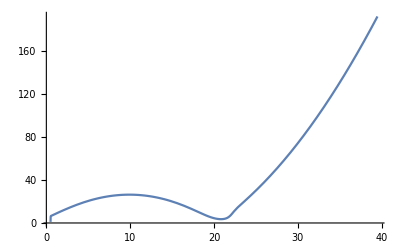

```mathematica
Plot[{A[r]/.sol,α[r]/.sol},{r,r0,rinf},PlotRange->All]
```

```mathematica
sBt=Solve[Etr==0,D[B[t,r],t]][[1]]//Simplify
```

{B^(1,0)[t,r]→1/4 ⅇ^(A[t,r]-B[t,r]) r P[t,r] Q[t,r]}

```mathematica
{sAr,sBr}=Collect[Solve[{Ett,Err}==0,D[{A[t,r],B[t,r]},r]][[1]],{r},FullSimplify]
```

{A^(0,1)[t,r]→(-1+ⅇ^(2 B[t,r]))/(2 r)+1/8 r (P[t,r]^2+Q[t,r]^2),B^(0,1)[t,r]→(1-ⅇ^(2 B[t,r]))/(2 r)+1/8 r (P[t,r]^2+Q[t,r]^2)}

```mathematica
EP1
```

-(2 ⅇ^(A[t,r]-B[t,r]) Q[t,r])/r-ⅇ^(A[t,r]-B[t,r]) Q[t,r] A^(0,1)[t,r]+ⅇ^(A[t,r]-B[t,r]) Q[t,r] B^(0,1)[t,r]-ⅇ^(A[t,r]-B[t,r]) Q^(0,1)[t,r]+P^(1,0)[t,r]

```mathematica
EP=EP1//.{sAr,sBr}//Simplify
EQ=EQ1//.{sAr,sBr}//Simplify
```

-(ⅇ^(A[t,r]-B[t,r]) (1+ⅇ^(2 B[t,r])) Q[t,r])/r-ⅇ^(A[t,r]-B[t,r]) Q^(0,1)[t,r]+P^(1,0)[t,r]

-(ⅇ^(A[t,r]-B[t,r]) (-1+ⅇ^(2 B[t,r])) P[t,r])/r-ⅇ^(A[t,r]-B[t,r]) P^(0,1)[t,r]+Q^(1,0)[t,r]

```mathematica
EP1//FullSimplify
EP//Simplify
```

-(ⅇ^(A[t,r]-B[t,r]) (Q[t,r] (2+r A^(0,1)[t,r]-r B^(0,1)[t,r])+r Q^(0,1)[t,r]))/r+P^(1,0)[t,r]

-(ⅇ^(A[t,r]-B[t,r]) (1+ⅇ^(2 B[t,r])) Q[t,r])/r-ⅇ^(A[t,r]-B[t,r]) Q^(0,1)[t,r]+P^(1,0)[t,r]

```mathematica
EQ1//FullSimplify
EQ
```

-ⅇ^(A[t,r]-B[t,r]) (P[t,r] (A^(0,1)[t,r]-B^(0,1)[t,r])+P^(0,1)[t,r])+Q^(1,0)[t,r]

-(ⅇ^(A[t,r]-B[t,r]) (-1+ⅇ^(2 B[t,r])) P[t,r])/r-ⅇ^(A[t,r]-B[t,r]) P^(0,1)[t,r]+Q^(1,0)[t,r]

```mathematica
EA
```

(1-ⅇ^(2 B[t,r]))/(2 r)+1/8 r (-P[t,r]^2-Q[t,r]^2)+A^(0,1)[t,r]

```mathematica
sostϕt
```

{ϕ0^(1,0)[t,r]→ⅇ^(A[t,r]-B[t,r]) P[t,r]}

```mathematica
Ethth=Collect[Exp[2B[t,r]-2A[t,r]]Eθθ//.Union[sBt,D[sBt,t],sPt,sQt]/.D[B[t,r],r]->D[A[t,r],r]+1/r+CP[t,r],{D[A[t,r],{r,2}],D[Q[t,r],r],D[P[t,r],r],CP[t,r]},FullSimplify]/.CP[t,r]->D[B[t,r],r]-(D[A[t,r],r]+1/r)
```

-(1+r A^(0,1)[t,r])/r^2+1/4 (-4/r+r P[t,r]^2+r Q[t,r]^2-4 A^(0,1)[t,r]) (-1/r-A^(0,1)[t,r]+B^(0,1)[t,r])-1/4 r P[t,r] P^(0,1)[t,r]-1/4 r Q[t,r] Q^(0,1)[t,r]+A^(0,2)[t,r]

```mathematica
Ethth-Exp[2B[t,r]-2A[t,r]]Eθθ//.Union[sBt,D[sBt,t],sPt,sQt]//Simplify
```

0

```mathematica
Unprotect[Power];
Power/:Format[Power[E,x_],FortranForm]:=exp[x]
Protect[Power];
sostFortran={A[t,r]->A,D[A[t,r],r]->drA,D[A[t,r],{r,2}]->drrA,B[t,r]->B,D[B[t,r],r]->drB,P[t,r]->P,D[P[t,r],r]->drP,Q[t,r]->Q,D[Q[t,r],r]->drQ};
```

```mathematica
FortranForm[Ethth/.sostFortran]
```

drrA - (drP*P*r)/4. - (drQ*Q*r)/4. - (1 + drA*r)/r**2 + ((-drA + drB - 1/r)*(-4*drA - 4/r + P**2*r + Q**2*r))/4.

```mathematica
FortranForm[(EP-D[P[t,r],t]//FullSimplify)/.sostFortran]
```

-((exp(A - B)*((1 + exp(2*B))*Q + drQ*r))/r)

```mathematica
FortranForm[(EQ-D[Q[t,r],t]//FullSimplify)/.sostFortran]
```

-((exp(A - B)*((-1 + exp(2*B))*P + drP*r))/r)

```mathematica
FortranForm[EA-D[A[t,r],r]/.sostFortran]
```

(1 - exp(2*B))/(2.*r) + ((-P**2 - Q**2)*r)/8.

```mathematica
FortranForm[EB-D[B[t,r],r]/.sostFortran]
```

(-1 + exp(2*B))/(2.*r) + ((-P**2 - Q**2)*r)/8.

```mathematica
Eθθ//.Union[sBt,D[sBt,t],sQt,sPt,{sAr,sBr,D[sAr,r]}]//Simplify
```

0

```mathematica
Clear[P,Q,A,B]
```

```mathematica
P[t_,r_]:=p0[t]+r^2 p2[t]+r^4 p4[r]
Q[t_,r_]:=q0[t]+r q1[t]+r^3 q3[t]
A[t_,r_]:=a0[t]+r^2 a2[t]+r^4 a4[t]
B[t_,r_]:=b0[t]+r^2 b2[t]+r^4 b4[t]
```

```mathematica
b0[t_]:=0
a0[t_]:=0
q0[t_]:=0
```

```mathematica
sb2=Solve[SeriesCoefficient[EB,{r,0,1}]==0,b2[t]][[1]]
sa2=Solve[(SeriesCoefficient[EA,{r,0,1}]/.sb2)==0,a2[t]][[1]]
```

{b2[t]→p0[t]^2/24}

{a2[t]→p0[t]^2/12}

```mathematica
Series[EP,{r,0,2}]//.Union[sb2,sa2]//Simplify
Series[EQ,{r,0,2}]//.Union[sb2,sa2]//Simplify
Series[EA,{r,0,4}]//.Union[sb2,sa2]//Simplify
Series[EB,{r,0,4}]//.Union[sb2,sa2]//Simplify
```

(-3 q1[t]+p0'[t])+(-5/24 p0[t]^2 q1[t]-5 q3[t]+p2'[t]) r^2+O[r]^3

(-1/12 p0[t]^3-2 p2[t]+q1'[t]) r+O[r]^3

(4 a4[t]-b4[t]-p0[t]^4/576-1/4 p0[t] p2[t]-q1[t]^2/8) r^3+O[r]^5

(5 b4[t]+p0[t]^4/576-1/4 p0[t] p2[t]-q1[t]^2/8) r^3+O[r]^5

```mathematica
A[t,r]/.sa2
B[t,r]/.sb2
```

1/12 r^2 p0[t]^2

1/24 r^2 p0[t]^2